```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"velocity tools","init.nb"}]];
```

## Numeric Algorithm V1 (Via Primal Variables)

-Graphics-

```mathematica
proj[u_]:=Projection[u,{1,0}]
```

```mathematica
FindBisection[F0_,F1_,x0_,x1_,maxSteps_:1000]:=Module[{
y0Old=proj[x0],y1Old=proj[x1],
k=0,δ=Infinity,thr=$MachineEpsilon,results={},
yOld,z0,z1},
(* Return {solution, results} pair where results is a [k x 4] array with coulumns for {δ, y1Old, y0Old, yOld} after each step *)
While[Abs[δ]>thr&&k<maxSteps,
k+=1;
(* Step 1 *)
yOld=(y0Old+y1Old)/2;
(* Step 2 *)
z0=Subscript[𝒩̂, F0][(yOld-x0)/Subscript[γ, F0][yOld-x0]]/.λ->0.5;
z1=-Subscript[𝒩̂, F1][(x1-yOld)/Subscript[γ, F1][x1-yOld]]/.λ->0.5;
(* Step 3 *)
δ=proj[z0+z1][[1]];
(* Step 4 *)
If[Abs[δ]>thr,
If[proj[x0][[1]]<proj[x1][[1]],(* <- this if statement is new *)
If[δ>0,
y1Old=yOld;,
y0Old=yOld;
],
If[δ>0,
y0Old=yOld;,
y1Old=yOld;
]
]
];
AppendTo[results,{δ,y1Old,y0Old,yOld}]
];
{yOld,results}
]
```

### Transport From Point

```mathematica
defVel[F1,1.5{{0,1},{1,0},{0,-1},{-1,0}}]
defVel[F0,{{1,1},-{1,1},{1,-1},{-1,1}}]
```

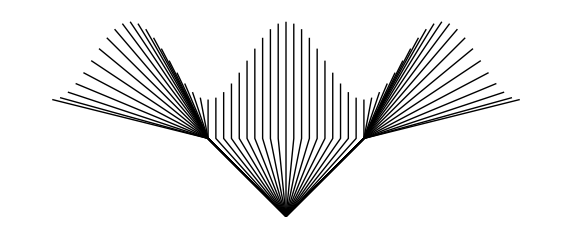

```mathematica
x0={0,-1.};

targets=Table[{p,1+0.5Cos[π p]},{p,-3,3,0.1}];

Show[Graphics@Table[
{y,r}=FindBisection[F0,F1,x0,targ];
Line[{x0,y,targ}],
{targ,targets}]]
```

### Derivation/Experiments

Warning: The code in this section was written while the algorithm was in development so certain segments will be inaccurate.

#### Numeric Algorithm V1 (Smooth)

```mathematica
First@Timing@Quiet@defVel[F0,1{Cos[t],Sin[t]}]
First@Timing@Quiet@defVel[F1,2{Cos[t],Sin[t]}]
```

0.1875

0.09375

```mathematica
x0={1,-1.};
x1={-1.,1};
y0Old=proj[x0];
y1Old=proj[x1];

δ=Infinity;
thr=$MachineEpsilon;
results={};
Monitor[
While[Abs[δ]>thr,
(* Step 1 *)
yOld=(y0Old+y1Old)/2;
(* Step 2 *)
z0=Subscript[𝒩̂, F0][(yOld-x0)/(Subscript[γ, F0][yOld-x0])];
z1=-Subscript[𝒩̂, F1][(x1-yOld)/(Subscript[γ, F1][x1-yOld])];
(* Step 3 *)
δ=proj[z0+z1][[1]];
(* Step 4 *)
If[δ!=0,
If[proj[x0][[1]]<proj[x1][[1]],
If[δ>0,
y1Old=yOld;,
y0Old=yOld;
],
If[δ>0,
y0Old=yOld;,
y1Old=yOld;
]
]
];
AppendTo[results,{δ,yOld}]
];
y0Old//N
,{δ,y0Old}//N]
```

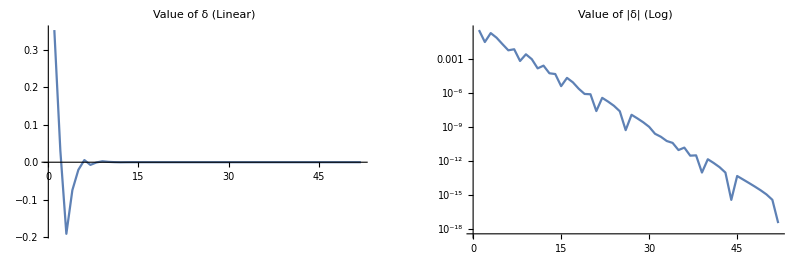

```mathematica
GraphicsRow[{
ListLinePlot[results[[;;,1]],PlotRange->All,
PlotLabel->"Value of δ (Linear)"],
ListLinePlot[Abs[results[[;;,1]]],PlotRange->All,ScalingFunctions->"Log",
PlotLabel->"Value of |δ| (Log)"]
}]
```

```mathematica
(* plot path during fist 10 steps of algorithm *)
ListAnimate@Table[Graphics[Line[{x0,xΣ,x1}],ImageSize->Small],{xΣ,results[[;;10,2]]}]
```

#### Numeric Algorithm V1 (Polyhedral)

```mathematica
Clear[x,y]
defVel[F0,{{1,0},{0,1},{-1,0},{0,-1}}]
defVel[F1,{{1,1},{1,-1},{-1,1},{-1,-1}}]
GraphicsRow[LabeledPolarHullPlot/@{F0,F1}]
```

Last::normal: Nonatomic expression expected at position 1 in Last[0].

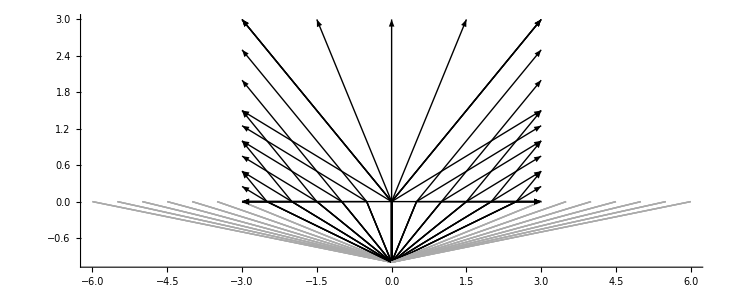

```mathematica
Show[Graphics[{
Arrowheads[Small],
Table[
Module[{x0={0,-1.},T=4,t=-.1,y0,v0,ζ0,ζ2s,v2s},
y0={t0,0};
t=Subscript[γ, F0][y0-x0];
v0=(y0-x0)/t;
(* Choose ζ0 ∈ Subscript[N, F0](v0) *)
ζ0=Subscript[𝒩̂, F0][v0](* points in normal cone properly scaled *);
(* calculate refracted angles with optimality conditions *)
ζ2s=Subscript[RefractedNormals, F1][ζ0];
v2s=Select[discretize/@(𝒩̂)_(F1^°)/@ζ2s,NonNegative@Last@#&];


If[T>Subscript[γ, F0][y0-x0],
{Black,Line[{x0,y0}],Tooltip[Arrow[{y0,(y0+(T-Subscript[γ, F0][y0-x0])#)}],{v0}]},
{Lighter@Gray,Line[{x0,y0}]}
]&/@v2s

],
{t0,-6,6,0.5}
]}],Axes->{True,False}]
```

```mathematica
Reverse[Show[{
Graphics[{Black,InfiniteLine[{0,0},{1,0}],Thick,Dashed,InfiniteLine[{0,0},{0,1}]}],
LabeledPolarPlot[F1,"(1)",TranslationTransform[#]@*ScalingTransform[{-1,-1}]],
Graphics[{Thick,Red,Arrow[{{0,0},#}]}]
},Axes->False,PlotRange->{1.5{-1,1},2{-0.5,1}},AspectRatio->{1,1},ImageSize->300]&/@Select[(F0^°)_pt,0<atan2[#]<π&]]
```

{-Graphics-,-Graphics-}

```mathematica
x0={0,-1.};
x1={1,1};
y0Old=proj[x0];
y1Old=proj[x1];

k=0;
δ=Infinity;
thr=$MachineEpsilon;
results={};
Monitor[
While[Abs[δ]>thr&&k<100,
k+=1;
(* Step 1 *)
yOld=(y0Old+y1Old)/2;
(* Step 2 *)
z0=Subscript[𝒩̂, F0][(yOld-x0)/Subscript[γ, F0][yOld-x0]]/.λ->.5;
z1=-Subscript[𝒩̂, F1][(x1-yOld)/Subscript[γ, F1][x1-yOld]]/.λ->.5;
(* Step 3 *)
δ=proj[z0+z1][[1]];
(* Step 4 *)
If[Abs[δ]>thr,
If[proj[x0][[1]]<proj[x1][[1]],
If[δ>0,
y1Old=yOld;,
y0Old=yOld;
],
If[δ>0,
y0Old=yOld;,
y1Old=yOld;
]
]
];
AppendTo[results,{δ,y1Old,y0Old,yOld}]
];
,{δ,y0Old}//N]
{y1Old,y0Old,yOld}//N
```

{{2.24265×10^-14,0.},{2.22045×10^-14,0.},{2.23155×10^-14,0.}}

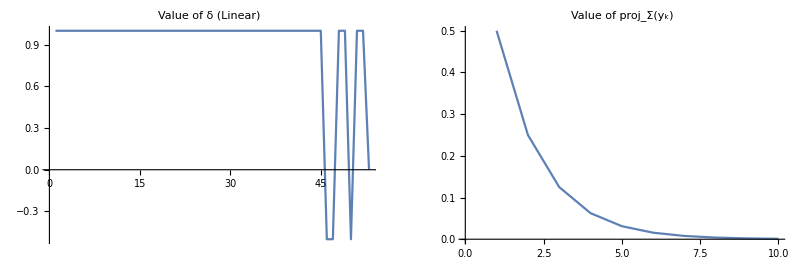

```mathematica
GraphicsRow[{
ListLinePlot[results[[;;,1]],PlotRange->All,
PlotLabel->"Value of δ (Linear)"],
ListLinePlot[results[[;;10,2,1]],PlotLabel->"Value of proj_Σ(y_k)"]
}]
```

```mathematica
TableForm[ArrayFlatten[{{List/@results[[;;,1]],results[[;;,2;;4,1]]}}],TableHeadings->{Range[1,Length[results]],{"δ","proj_Σ(y_1^Old)","proj_Σ(y_2^Old)","proj_Σ(y)"}}]
```

| δ | proj_Σ(y_1^Old) | proj_Σ(y_2^Old) | proj_Σ(y)
1 | 1 | 0.5 | 0. | 0.5
2 | 1 | 0.25 | 0. | 0.25
3 | 1 | 0.125 | 0. | 0.125
4 | 1 | 0.0625 | 0. | 0.0625
5 | 1 | 0.03125 | 0. | 0.03125
6 | 1 | 0.015625 | 0. | 0.015625
7 | 1 | 0.0078125 | 0. | 0.0078125
8 | 1 | 0.00390625 | 0. | 0.00390625
9 | 1 | 0.00195313 | 0. | 0.00195313
10 | 1 | 0.000976563 | 0. | 0.000976563
11 | 1 | 0.000488281 | 0. | 0.000488281
12 | 1 | 0.000244141 | 0. | 0.000244141
13 | 1 | 0.00012207 | 0. | 0.00012207
14 | 1 | 0.0000610352 | 0. | 0.0000610352
15 | 1 | 0.0000305176 | 0. | 0.0000305176
16 | 1 | 0.0000152588 | 0. | 0.0000152588
17 | 1 | 7.62939×10^-6 | 0. | 7.62939×10^-6
18 | 1 | 3.8147×10^-6 | 0. | 3.8147×10^-6
19 | 1 | 1.90735×10^-6 | 0. | 1.90735×10^-6
20 | 1 | 9.53674×10^-7 | 0. | 9.53674×10^-7
21 | 1 | 4.76837×10^-7 | 0. | 4.76837×10^-7
22 | 1 | 2.38419×10^-7 | 0. | 2.38419×10^-7
23 | 1 | 1.19209×10^-7 | 0. | 1.19209×10^-7
24 | 1 | 5.96046×10^-8 | 0. | 5.96046×10^-8
25 | 1 | 2.98023×10^-8 | 0. | 2.98023×10^-8
26 | 1 | 1.49012×10^-8 | 0. | 1.49012×10^-8
27 | 1 | 7.45058×10^-9 | 0. | 7.45058×10^-9
28 | 1 | 3.72529×10^-9 | 0. | 3.72529×10^-9
29 | 1 | 1.86265×10^-9 | 0. | 1.86265×10^-9
30 | 1 | 9.31323×10^-10 | 0. | 9.31323×10^-10
31 | 1 | 4.65661×10^-10 | 0. | 4.65661×10^-10
32 | 1 | 2.32831×10^-10 | 0. | 2.32831×10^-10
33 | 1 | 1.16415×10^-10 | 0. | 1.16415×10^-10
34 | 1 | 5.82077×10^-11 | 0. | 5.82077×10^-11
35 | 1 | 2.91038×10^-11 | 0. | 2.91038×10^-11
36 | 1 | 1.45519×10^-11 | 0. | 1.45519×10^-11
37 | 1 | 7.27596×10^-12 | 0. | 7.27596×10^-12
38 | 1 | 3.63798×10^-12 | 0. | 3.63798×10^-12
39 | 1 | 1.81899×10^-12 | 0. | 1.81899×10^-12
40 | 1 | 9.09495×10^-13 | 0. | 9.09495×10^-13
41 | 1 | 4.54747×10^-13 | 0. | 4.54747×10^-13
42 | 1 | 2.27374×10^-13 | 0. | 2.27374×10^-13
43 | 1 | 1.13687×10^-13 | 0. | 1.13687×10^-13
44 | 1 | 5.68434×10^-14 | 0. | 5.68434×10^-14
45 | 1 | 2.84217×10^-14 | 0. | 2.84217×10^-14
46 | -0.5 | 2.84217×10^-14 | 1.42109×10^-14 | 1.42109×10^-14
47 | -0.5 | 2.84217×10^-14 | 2.13163×10^-14 | 2.13163×10^-14
48 | 1 | 2.4869×10^-14 | 2.13163×10^-14 | 2.4869×10^-14
49 | 1 | 2.30926×10^-14 | 2.13163×10^-14 | 2.30926×10^-14
50 | -0.5 | 2.30926×10^-14 | 2.22045×10^-14 | 2.22045×10^-14
51 | 1 | 2.26485×10^-14 | 2.22045×10^-14 | 2.26485×10^-14
52 | 1 | 2.24265×10^-14 | 2.22045×10^-14 | 2.24265×10^-14
53 | 0. | 2.24265×10^-14 | 2.22045×10^-14 | 2.23155×10^-14

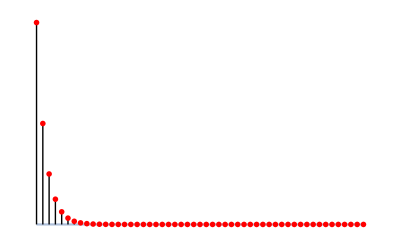

```mathematica
Show[{
Plot[0,{x,1,Length[results]},Axes->False,PlotStyle->Opacity[0.5]],
Graphics[{Line[{{#1,#2},{#1,#4}}],Red,PointSize[0.01],Point[{#1,#3}]}]&@@@ArrayFlatten[{{List/@Range[1,Length[results]],results[[;;,{2,4,3},1]]}}]
},PlotRange->All]
```

```mathematica
{y1Old,y0Old,yOld}//N
```

{{-2.,0.},{-2.,0.},{-2.,0.}}

```mathematica
k
```

100

```mathematica
y0Old
```

{0.,0.}

```mathematica
δ
```

-1.

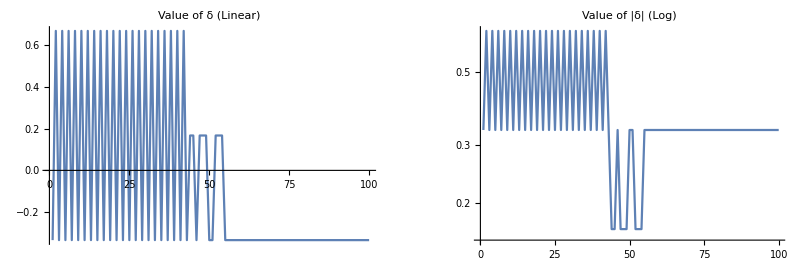

```mathematica
GraphicsRow[{
ListLinePlot[results[[;;,1]],PlotRange->All,
PlotLabel->"Value of δ (Linear)"],
ListLinePlot[Abs[results[[;;,1]]],PlotRange->All,ScalingFunctions->"Log",
PlotLabel->"Value of |δ| (Log)"]
}]
```

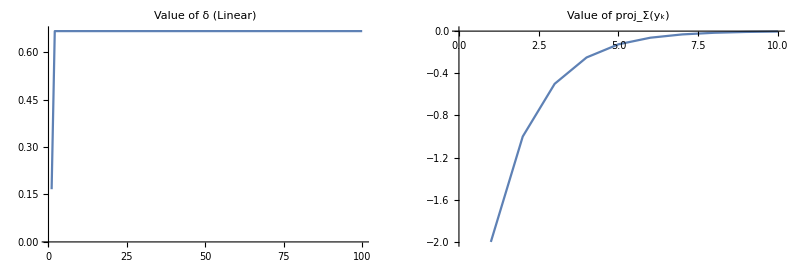

```mathematica
GraphicsRow[{
ListLinePlot[results[[;;,1]],PlotRange->All,
PlotLabel->"Value of δ (Linear)"],
ListLinePlot[results[[;;10,2,1]],PlotLabel->"Value of proj_Σ(y_k)"]
}]
```

```mathematica
(* plot path during fist 10 steps of algorithm *)
ListAnimate@Table[Graphics[Line[{x0,xΣ,x1}],ImageSize->Small],{xΣ,results[[;;10,2]]}]
```

```mathematica
First@Timing@Quiet@defVel[F0,{{-1,-1},{-1,1},{1,-1},{1,1},{2,0},{-1.5,0}}]
First@Timing@Quiet@defVel[F1,1.5{{0,1},{1,0},{0,-1},{-1,0}}]
(*First@Timing@Quiet@defVel[F0,{{1,1},-{1,1},{1,-1},{-1,1}}]*)
GraphicsRow[LabeledPolarHullPlot/@{F0,F1}]
```

0.03125

0.

-Graphics-

```mathematica
RandomReal[{0,1}]
```

```mathematica
x0={0,-2.};
x1={-6,1.};
y0Old=proj[x0];
y1Old=proj[x1];

k=0;
δ=Infinity;
thr=$MachineEpsilon;
results={};
Monitor[
While[Abs[δ]>thr&&k<100,
k+=1;
(* Step 1 *)
yOld=(y0Old+y1Old)/2;
(* Step 2 *)
z0=Subscript[𝒩̂, F0][(yOld-x0)/Subscript[γ, F0][yOld-x0]];
If[Not@FreeQ[z0,λ],Echo[{k,"z0",z0}];z0=z0/.λ->.5];
z1=-Subscript[𝒩̂, F1][(x1-yOld)/Subscript[γ, F1][x1-yOld]];
If[Not@FreeQ[z1,λ],Echo[{k,"z1",z1}];z1=z1/.λ->.5];
(* Step 3 *)
δ=proj[z0+z1][[1]];
(*Echo[{yOld,y0Old,y1Old,z0,z1,δ}];*)
(* Step 4 *)
If[Abs[δ]>thr,
If[δ>0,
y1Old=yOld;,
y0Old=yOld;
]
];
AppendTo[results,{δ,yOld}]
];
,{k,δ,y0Old}//N]
yOld
```

{48,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{49,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{50,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{51,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{52,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{53,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{54,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{55,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{56,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{57,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{58,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{59,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{60,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{61,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{62,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{63,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{64,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{65,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{66,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{67,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{68,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{69,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{70,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{71,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{72,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{73,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{74,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{75,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{76,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{77,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{78,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{79,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{80,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{81,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{82,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{83,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{84,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{85,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{86,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{87,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{88,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{89,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{90,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{91,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{92,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{93,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{94,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{95,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{96,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{97,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{98,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{99,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{100,z1,{0.666667 (1-λ)-0.666667 λ,-0.666667 (1-λ)-0.666667 λ}}

{-6.,0.}

```mathematica
z0
```

{-0.666667,0.333333}

```mathematica
z1
```

{0.666667,-0.666667}

```mathematica
Subscript[γ, F0][yOld-x0]+Subscript[γ, F1][x1-yOld]
```

5.33333

```mathematica
Subscript[γ, F0][{-6,0}-x0]+Subscript[γ, F1][x1-{-6,0}]
```

5.33333

```mathematica
δ
```

0.

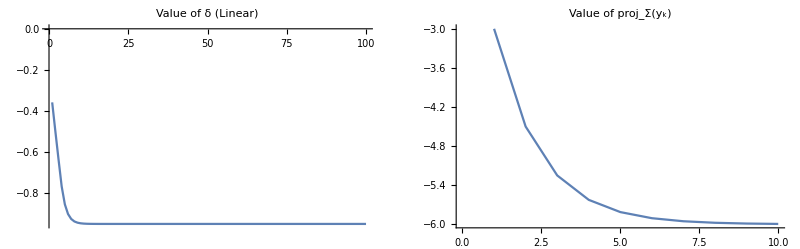

```mathematica
GraphicsRow[{
ListLinePlot[results[[;;,1]],PlotRange->All,
PlotLabel->"Value of δ (Linear)"],
ListLinePlot[results[[;;10,2,1]],PlotLabel->"Value of proj_Σ(y_k)"]
}]
```

```mathematica
(* plot path during fist 10 steps of algorithm *)
ListAnimate@Table[Graphics[Line[{x0,xΣ,x1}],ImageSize->Small],{xΣ,results[[;;10,2]]}]
```

Part::take: Cannot take positions 1 through 10 in {{0.,{-3.,0.}}}.

Table::iterb: Iterator {xΣ,{{0.,{-3.,0.}}}⟦1;;10,2⟧} does not have appropriate bounds.

ListAnimate[Table[-Graphics-,{xΣ,{{0.,{-3.,0.}}}⟦1;;10,2⟧}]]

## Numeric Algorithm V2 (Using Duality)

This algorithm is currently a work in progress.

-Graphics-

### Derivation

#### Numeric Algorithm V2 (Smooth)

```mathematica
First@Timing@Quiet@defVel[F0,1{Cos[t],Sin[t]}]
First@Timing@Quiet@defVel[F1,2{Cos[t],Sin[t]}]
```

0.015625

0.015625

```mathematica
x0={-1,-1}//N;
x1={1,1}//N;
y0Old=proj[x0];
y1Old=proj[x1];

k=0;
δ=Infinity;
thr=$MachineEpsilon;
results={};
Monitor[
While[Abs[δ]>thr&&k<=1*^4,
k+=1;
(* Step 1 *)
yOld=(y0Old+y1Old)/2;
(* Step 2 *)
z0=Subscript[𝒩̂, F0][(yOld-x0)/(Subscript[γ, F0][yOld-x0])];
z1=-Subscript[𝒩̂, F1][(x1-yOld)/(Subscript[γ, F1][x1-yOld])];
(* Step 3 *)
δ=proj[z0+z1][[1]];
(* Step 4 *)
If[δ!=0,
If[δ>0,
v1=(𝒩̂)_(F1^°)[z1];
y1Old=δ proj[v1];,
v0=(𝒩̂)_(F0^°)[z0];
y0Old=δ proj[v0];
]
];
AppendTo[results,{δ,yOld,y1Old,y0Old}]
];
y0Old//N
,{δ,yOld,y0Old,y1Old,k}//N]
```

{-0.0464664,0.}

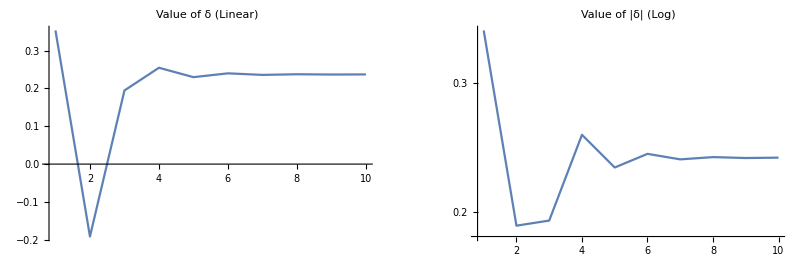

```mathematica
maxK=10;
GraphicsRow[{
ListLinePlot[results[[;;maxK,1]],PlotRange->All,
PlotLabel->"Value of δ (Linear)"],
ListLinePlot[Abs[results[[;;maxK,1]]],PlotRange->All,ScalingFunctions->"Log",
PlotLabel->"Value of |δ| (Log)"]
}]
```

## Exact Solution Derivation

```mathematica
First@Timing@Quiet@defVel[F0,{Cos[t],Sin [t]}]
First@Timing@Quiet@defVel[F1,2{Cos[t],Sin[t]}]

x0={-1,-1};
x1={1,1};
```

0.15625

0.078125

We can find the scaled normal cone of F1 from x0 at any point in space.

```mathematica
(𝒩̂)_(F1^°)[{x,y}-x0]
```

{(2 (1+x))/(√((1+x)^2+(1+y)^2)),(2 (1+y))/(√((1+x)^2+(1+y)^2))}

This plot shows the x-component of the dual vectors ζ_0 and ζ_1 along the interface Σ. The sum of these components is shown in green.

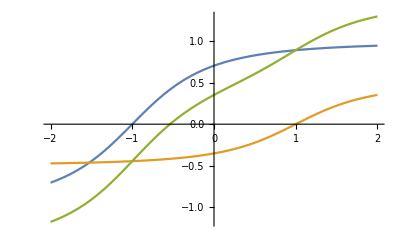

```mathematica
Plot[{
Subscript[𝒩̂, F0][{x,0}-x0][[1]],
-Subscript[𝒩̂, F1][x1-{x,0}][[1]],
Subscript[𝒩̂, F0][{x,0}-x0][[1]]-Subscript[𝒩̂, F1][x1-{x,0}][[1]]
},{x,-2,2}]
```

Where these curves are equal opposites is optimal crossing point, which can be solved exactly.

```mathematica
Subscript[𝒩̂, F0][{x,0}-x0][[1]]-Subscript[𝒩̂, F1][x1-{x,0}][[1]]
x/.Solve[%==0,x]
xOpt=First@Select[%,Im[#]==0&]
%//N
```

-(1-x)/(2 √(1+(1-x)^2))+(1+x)/(√(1+(1+x)^2))

{-1/6 √(6+(5967-216 √519)^(1/3)+3 (221+8 √519)^(1/3))+1/2 √(4/3-1/9 (5967-216 √519)^(1/3)-1/3 (221+8 √519)^(1/3)+20/(√(6+(5967-216 √519)^(1/3)+3 (221+8 √519)^(1/3))))}

-1/6 √(6+(5967-216 √519)^(1/3)+3 (221+8 √519)^(1/3))+1/2 √(4/3-1/9 (5967-216 √519)^(1/3)-1/3 (221+8 √519)^(1/3)+20/(√(6+(5967-216 √519)^(1/3)+3 (221+8 √519)^(1/3))))

-0.538264

What is the optimal travel time?

```mathematica
xΣ={xOpt,0};
t0=Subscript[γ, F0][xΣ-x0];
t1=Subscript[γ, F1][x1-xΣ];
T=t0+t1//N
```

2.01882

How does this fit in the previously computable solutions?

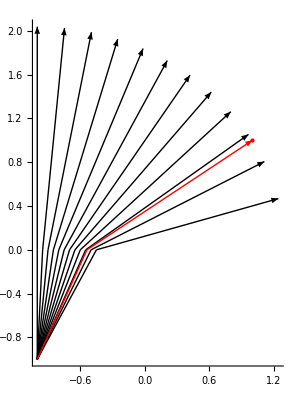

```mathematica
raytracePlt=Show[Graphics[{
Arrowheads[Small],
Table[
Module[{T=T,t,y0,v0,ζ0,ζ2s,v2s},
y0={t0,0};
t=Subscript[γ, F0][y0-x0];
v0=(y0-x0)/t;
(* Choose ζ0 ∈ Subscript[N, F0](v0) *)
ζ0=Subscript[𝒩̂, F0][v0](* properly scaled normal cone points *);
(* calculate refracted angles with optimality conditions *)
ζ2s=Subscript[RefractedNormals, F1][ζ0];
v2s=discretize/@Select[(𝒩̂)_(F1^°)/@ζ2s,NonNegative@Last@#&];


If[T>Subscript[γ, F0][y0-x0],
{Black,Line[{x0,y0}],Arrow[{y0,(y0+(T-Subscript[γ, F0][y0-x0])#)}]},
{Lighter@Gray,Line[{x0,y0}],Black,Arrow[{x0,x0+T v0}]}
]&/@v2s

],
{t0,-1,.5,0.05}
]},Axes->True]];
Show[raytracePlt,Graphics[{Red,Arrow[{x0,xΣ,x1}],Point[{1,1}]}]]
```